```mathematica
(***************Question 10***************)(***Show that x3 is O(x4) but that x4 is not O(x3)***)
```

```mathematica
f=x^3
```

x^3

```mathematica
g=x^4
```

x^4

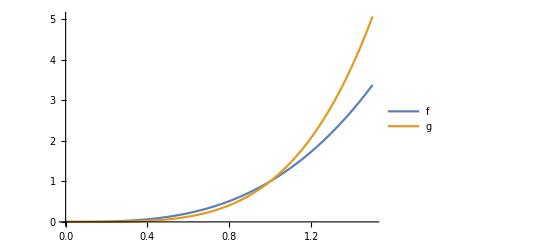

```mathematica
Plot[{f,g},{x,0,1.5},PlotLegends->"Expressions"]
```

```mathematica
(**Convincing evidence that for k=1 and C=1 witness, x^3 is O(x^4)**)
```

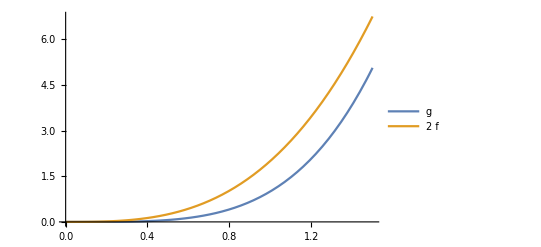

```mathematica
Plot[{g,2*f},{x,0,1.5},PlotLegends->"Expressions"]
```

```mathematica
(**For arbitrary number x, no such C and k exist that x>k and x^4 < Cx^3, therefore x^4 is NOT O(x^3)**)
```

```mathematica
(***************Question 14***************)
(***(a) g(x)=x2***)
f14= x^3
```

x^3

```mathematica
g14a = x^2
```

x^2

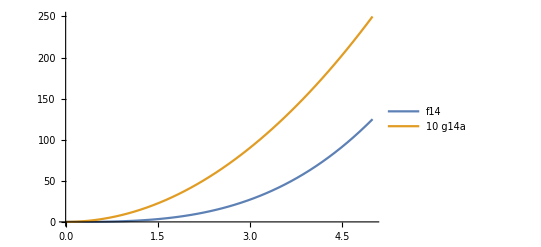

```mathematica
Plot[{f14,10*g14a},{x,0,5},PlotLegends->"Expressions"]
```

```mathematica
(***For arbitrary number x, no such C and k exist that x>k and x^3 < Cx^2, therefore x^3 is NOT O(x^2)***)
```

```mathematica
(***(b) g(x)=x3***)
g14b = x^3
```

x^3

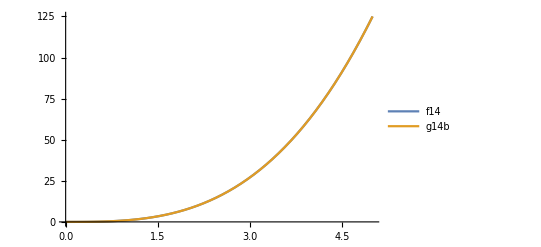

```mathematica
Plot[{f14,g14b},{x,0,5},PlotLegends->"Expressions"]
```

```mathematica
(***Since the two lines are same, when C=1 and k=0, the absolute value of f(x) is always equal to g(x), x^3 is O(x^3)***)
```

```mathematica
(***(c) g(x)=x2+x3***)
```

```mathematica
g14c=x^2 + x^3
```

x^2+x^3

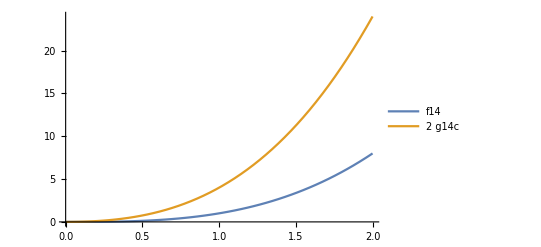

```mathematica
Plot[{f14,2*g14c},{x,0,2},PlotLegends->"Expressions"]
```

```mathematica
(***For C=2 and k=0 witness, x^3 is O(x^2 + x^3)***)
```

```mathematica
(***************Question 20***************)
(***log(n+1) and log(n2+1) is O(log n)***)
```

```mathematica
f1=Log[x+1]
```

Log[1+x]

```mathematica
f2=Log[x^2+1]
```

Log[1+x^2]

```mathematica
g20=Log[x]
```

Log[x]

```mathematica
Manipulate[Plot[{f1,c*g20},{x,0,5},PlotRange->Automatic,PlotLegends->"Expressions"],{n,1,20,1},{c,1,30}]
```

```mathematica
(***Sufficient evidence to say there exist C and k witness that log(n+1) is O(log n)***)
```

```mathematica
Manipulate[Plot[{f2,c*g20},{x,0,5},PlotRange->Automatic,PlotLegends->"Expressions"],{n,1,20,1},{c,1,30}]
```

```mathematica
(***Sufficient evidence to say there exist C and k witness that log(n2+1) is O(log n)***)
```